## Verify and Plot

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
getRegionSAS[sas_]:=And@@(GreaterEqual[#,0]&/@sas);
verifyResults[benchmark_,plot_,plotRange_,verifyTimeLimit_]:= Module[
{systemPath,xvarSet,yvarSet,zvarSet,s1,s2,hPath,hData,h,hHomo,sdpTime,verifyTime,totalTime,result,flag,flagHomo,i},
systemPath=FileNameJoin[{".","Results","problem",StringJoin[benchmark,".txt"]}];
{xvarSet,yvarSet,zvarSet,s1,s2} = ReadList[systemPath];
Print["x Variables: ",xvarSet];
Print["y Variables: ",yvarSet];
Print["z Variables: ",zvarSet];
Print["S1: ",s1];
Print["S2: ",s2];

Print["Verifying results (CAV20 method)..."];
flag =1;
hPath=FileNameJoin[{".","Results","sufficient",StringJoin[benchmark,".txt"]}];
hData=ReadList[hPath,{Expression,Expression},RecordSeparators-> "\n"];

(*Length(hData)== 1 if the degree of the template is fixed*)
h = hData[[1]][[1]];
sdpTime = hData[[1]][[2]];
result=Timing[TimeConstrained[myVerify[xvarSet, yvarSet, zvarSet, s1,s2,h],verifyTimeLimit,2]];
verifyTime=result[[1]];
totalTime = sdpTime+verifyTime;
If[result[[2]]== 0,
Print[Style["Numerical Errors Detected.",Red]];
flag=0;
];
If[result[[2]]== 1,
Print[Style["Valid solution.",Green]];
Print["h",h]
];
If[result[[2]]== 2,
Print[Style["Verify out of time.",Red]];
Print[h]
];
Print["SDP Time: ",sdpTime ];
Print["verify Time: ",verifyTime ];
Print["Total Time: ",totalTime ];

Print["Verifying results (homogenization)..."];
hPath=FileNameJoin[{".","Results","homo",StringJoin[benchmark,".txt"]}];
hData=ReadList[hPath,{Expression,Expression},RecordSeparators-> "\n"];
flagHomo=1;
(*Length(hData)== 1 if the degree of the template is fixed*)
hHomo = hData[[1]][[1]];
sdpTime = hData[[1]][[2]];
result=Timing[TimeConstrained[myVerifyHomo[xvarSet, yvarSet, zvarSet, s1,s2,hHomo],verifyTimeLimit,2]];
verifyTime=result[[1]];
totalTime = sdpTime+verifyTime;
If[result[[2]]== 0,
Print[Style["Numerical Errors Detected.",Red]];
flagHomo=0
];
If[result[[2]]== 1,
Print[Style["Valid solution.",Green]];
Print["hHomo:",hHomo]
];
If[result[[2]]== 2,
Print[Style["Verify out of time.",Red]];
Print[hHomo]
];
Print["SDP Time: ",sdpTime ];
Print["verify Time: ",verifyTime ];
Print["Total Time: ",totalTime ];

If[ plot== 1,
If[Length[xvarSet]== 2,myPlot2D[xvarSet,yvarSet,zvarSet,plotRange,s1,s2,If[flag== 0,-1,h],If[flagHomo== 0,-1,hHomo]]];
If[Length[xvarSet]== 3,myPlot3D[xvarSet,yvarSet,zvarSet,plotRange,s1,s2,If[flag== 0,-1,h],If[flagHomo== 0,-1,hHomo]]];
]
]

myVerify [xvarSet_,yvarSet_,zvarSet_,s1_,s2_,h_]:= Module[
{lambda,s1Cons,s2Cons,bcLie,cond1,cond2,timev},
timev=Now;
s1Cons = Or@@(getRegionSAS[#]&/@s1);
s2Cons = Or@@(getRegionSAS[#]&/@s2);
cond1 = FindInstance[h-1< 0&&s1Cons,Join[xvarSet,yvarSet]];
cond2 =FindInstance[-h-1<0&&s2Cons,Join[xvarSet,zvarSet]];
Print[cond1,cond2];
If[Length[cond1]+Length[cond2]==0, (*no counter-example is found*)
Return[1],
Return[0]];
]
myVerifyHomo [xvarSet_,yvarSet_,zvarSet_,s1_,s2_,hHomo_]:= Module[
{lambda,s1Cons,s2Cons,bcLie,cond1,cond2,timev},
timev=Now;
s1Cons = Or@@(getRegionSAS[#]&/@s1);
s2Cons = Or@@(getRegionSAS[#]&/@s2);
cond1 = FindInstance[hHomo≤  0&&s1Cons,Join[xvarSet,yvarSet]];
cond2 =FindInstance[-hHomo≤  0&&s2Cons,Join[xvarSet,zvarSet]];
Print[cond1,cond2];
If[Length[cond1]+Length[cond2]==0, (*no counter-example is found*)
Return[1],
Return[0]];
]

myPlot2D [xvarSet_,yvarSet_,zvarSet_,xvarRange_,s1_,s2_,h_,hHomo_]:= Module[
{ranges,s1Cons,s2Cons,s1Plot,s2Plot,hPlot,hHomoPlot},
Print["Plot2d..."];
ranges=Sequence @@ MapThread[Prepend,{xvarRange,xvarSet}];
s1Cons = Or@@(getRegionSAS[#]&/@s1);
s2Cons = Or@@(getRegionSAS[#]&/@s2);
Print[s1Cons];
Print[s2Cons];
Print[h];
Print[hHomo];
(*s1Cons=And@@Thread[GreaterEqualThan[0][s1]];s2Cons=And@@Thread[GreaterEqualThan[0][s2]];*)
s1Plot=RegionPlot[Resolve[Exists[yvarSet,s1Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None ,PlotPoints-> 100];
s2Plot=RegionPlot[Resolve[Exists[zvarSet,s2Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.915, 0.3325, 0.2125]},BoundaryStyle->None,PlotPoints-> 100];

hPlot=RegionPlot[h-1≥  0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[1, 0.75, 0]},BoundaryStyle-> {RGBColor[1, 0.75, 0]},PlotPoints-> 100];
hHomoPlot=RegionPlot[hHomo≥ 0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[0.363898, 0.618501, 0.782349]},BoundaryStyle->{RGBColor[0.363898, 0.618501, 0.782349]},PlotPoints-> 100];
Print[Show[s1Plot,s2Plot,hPlot,hHomoPlot, FrameLabel->xvarSet]]
]


(*inefficient, use other tools*)
myPlot3D [xvarSet_,yvarSet_,zvarSet_,xvarRange_,s1_,s2_,h_,hHomo_]:= Module[
{ranges,s1Cons,s2Cons,s1Plot,s2Plot,hPlot,hHomoPlot},
Print["Plot3D..."];
ranges=Sequence @@ MapThread[Prepend,{xvarRange,xvarSet}];
ranges=Sequence @@ MapThread[Prepend,{xvarRange,xvarSet}];
s1Cons = Or@@(getRegionSAS[#]&/@s1);
s2Cons = Or@@(getRegionSAS[#]&/@s2);
s1Plot=RegionPlot3D[Resolve[Exists[yvarSet,s1Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]},BoundaryStyle->None ,PlotPoints-> 100];
s2Plot=RegionPlot3D[Resolve[Exists[zvarSet,s2Cons],Reals],Evaluate[ranges],PlotStyle->{Opacity[0.65],RGBColor[0.915, 0.3325, 0.2125]},BoundaryStyle->None,PlotPoints-> 100];
hPlot=RegionPlot3D[h-1≥  0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[1, 0.75, 0]},BoundaryStyle-> {RGBColor[1, 0.75, 0]},PlotPoints-> 100];
hHomoPlot=RegionPlot3D[hHomo≥ 0,Evaluate[ranges],PlotStyle->{Opacity[0.15],RGBColor[0.363898, 0.618501, 0.782349]},BoundaryStyle->{RGBColor[0.363898, 0.618501, 0.782349]},PlotPoints-> 100];
Print[Show[s1Plot,s2Plot,hPlot,hHomoPlot, FrameLabel->xvarSet]]
];
```

## Benchmarks

### 2-d benchmarks

2d_ex4

x Variables: {x,y}

y Variables: {y0}

z Variables: {z0}

S1: {{27-x^3-y^3}}

S2: {{-16+x y,x,y}}

Verifying results (CAV20 method)...

{}{}

Valid solution.

h16.5701-0.513552 x+0.612877 x^2-0.521846 x^3-0.513552 y-0.554923 x y+0.612877 y^2-0.521846 y^3

SDP Time: 0.1058

verify Time: 0.242203

Total Time: 0.348003

Verifying results (homogenization)...

{{x→0,y→0,y0→0}}{}

Numerical Errors Detected.

SDP Time: 0.35966

verify Time: 0.008853

Total Time: 0.368513

Plot2d...

27-x^3-y^3≥0

-16+x y≥0&&x≥0&&y≥0

16.5701-0.513552 x+0.612877 x^2-0.521846 x^3-0.513552 y-0.554923 x y+0.612877 y^2-0.521846 y^3

-1

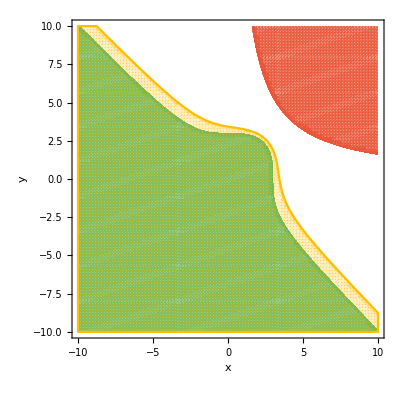

```mathematica
benchmarkname = "2d_ex4";
Print[benchmarkname];
verifytimelimit=1; (*verification time limit*)
plot =1; (*whether to plot(=1) or not (=0)*)
plotRange = {{-10,10},{-10,10}};
verifyResults[benchmarkname,plot,plotRange,verifytimelimit];
```

2d_ex2

x Variables: {x,y}

y Variables: {y0}

z Variables: {z0}

S1: {{3.8025-x^2+0.1 y^2,y,0.91-2. x+x^2+y^2,-0.1025+2. x+x^2+y^2},{-0.0975+2. x-x^2-y^2,0.91-2. x+x^2+y^2,-0.1025+2. x+x^2+y^2},{-0.96-2. x-x^2-y^2}}

S2: {{3.8025-x^2+0.1 y^2,-y,0.91+2. x+x^2+y^2,-0.1025-2. x+x^2+y^2},{-0.0975-2. x-x^2-y^2,0.91+2. x+x^2+y^2,-0.1025-2. x+x^2+y^2},{-0.96+2. x-x^2-y^2}}

Verifying results (CAV20 method)...

Divide::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0``-1.033720558418622 ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0``-2.1281701179540065 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Divide::infy: Infinite expression 1/(0``-105.58740947062313) encountered.

Divide::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

{}{}

Valid solution.

h-0.0000384917+23752.7 x+0.0000641893 x^2-53695.7 x^3+25613.9 x^5+0.000582623 x^7+3772.7 y+0.00124627 x y+58990.7 x^2 y-0.0029296 x^3 y-128320. x^4 y+0.00117382 x^5 y+64135.3 x^6 y+0.00157375 y^2+162312. x y^2-0.000721805 x^2 y^2-463933. x^3 y^2+0.00049074 x^4 y^2+263374. x^5 y^2+114532. y^3+0.0382177 x y^3-795938. x^2 y^3-0.0239912 x^3 y^3+648208. x^4 y^3+0.00189383 y^4+3.77339×10^6 x y^4-0.0394512 x^2 y^4-237225. x^3 y^4+721418. y^5-0.0155565 x y^5+696760. x^2 y^5+0.0370165 y^6-857549. x y^6+1.35328×10^6 y^7

SDP Time: 0.204703

verify Time: 6.63777

Total Time: 6.84247

Verifying results (homogenization)...

Valid solution.

hHomo:-0.00156347+12.7783 x-0.0143794 x^2-31.7337 x^3+0.0243557 x^4+19.5358 x^5-0.0113966 x^6-2.62705 x^7+1.95776 y-0.00408277 x y+1.99071 x^2 y+0.0378826 x^3 y-10.1989 x^4 y-0.0297712 x^5 y+5.44196 x^6 y+0.00317511 y^2+25.3843 x y^2+0.0295814 x^2 y^2+23.6338 x^3 y^2-0.0230454 x^4 y^2-4.20066 x^5 y^2+11.585 y^3-0.120597 x y^3-10.8655 x^2 y^3+0.0360004 x^3 y^3+17.7813 x^4 y^3-0.0322086 y^4+28.4969 x y^4-0.00258695 x^2 y^4-2.90775 x^3 y^4+16.2252 y^5+0.0504447 x y^5+24.5922 x^2 y^5-0.0103197 y^6+0.120085 x y^6+12.5399 y^7

SDP Time: 2.78085

verify Time: 7.50308

Total Time: 10.2839

Plot2d...

(3.8025-x^2+0.1 y^2≥0&&y≥0&&0.91-2. x+x^2+y^2≥0&&-0.1025+2. x+x^2+y^2≥0)||(-0.0975+2. x-x^2-y^2≥0&&0.91-2. x+x^2+y^2≥0&&-0.1025+2. x+x^2+y^2≥0)||-0.96-2. x-x^2-y^2≥0

(3.8025-x^2+0.1 y^2≥0&&-y≥0&&0.91+2. x+x^2+y^2≥0&&-0.1025-2. x+x^2+y^2≥0)||(-0.0975-2. x-x^2-y^2≥0&&0.91+2. x+x^2+y^2≥0&&-0.1025-2. x+x^2+y^2≥0)||-0.96+2. x-x^2-y^2≥0

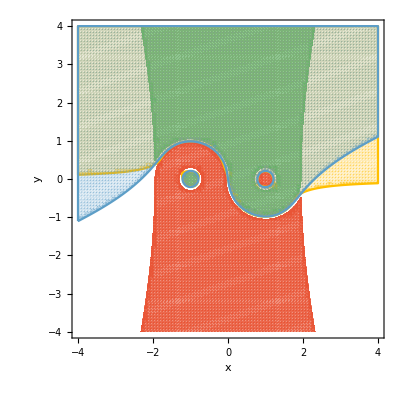

```mathematica
benchmarkname = "2d_ex2";
Print[benchmarkname];
verifytimelimit=600; (*verification time limit*)
plot =1; (*whether to plot(=1) or not (=0)*)
plotRange = {{-4,4},{-4,4}};
verifyResults[benchmarkname,plot,plotRange,verifytimelimit];
```

2d_ex2mod

x Variables: {x,y}

y Variables: {y0}

z Variables: {z0}

S1: {{4.-x^2,y,0.91-2. x+x^2+y^2,-0.1025+2. x+x^2+y^2},{-0.0975+2. x-x^2-y^2,0.91-2. x+x^2+y^2,-0.1025+2. x+x^2+y^2},{-0.96-2. x-x^2-y^2}}

S2: {{4.-x^2,-y,0.91+2. x+x^2+y^2,-0.1025-2. x+x^2+y^2},{-0.0975-2. x-x^2-y^2,0.91+2. x+x^2+y^2,-0.1025-2. x+x^2+y^2},{-0.96+2. x-x^2-y^2}}

Verifying results (CAV20 method)...

{}{}

Valid solution.

h969.624 x-2452.87 x^3+1556.68 x^5-232.478 x^7+135.649 y+151.838 x^2 y-714.928 x^4 y+370.679 x^6 y+1554.72 x y^2+2213.43 x^3 y^2-271.135 x^5 y^2+702.615 y^3-1154.06 x^2 y^3+1694.4 x^4 y^3+1071.26 x y^4+2.62479 x^3 y^4+868.715 y^5+1816.08 x^2 y^5+9.46532 x y^6+681.475 y^7

SDP Time: 0.170965

verify Time: 4.7404

Total Time: 4.91137

Verifying results (homogenization)...

Divide::infy: Infinite expression 1/(0``-1.8798305151852566) encountered.

Infinity::indet: Indeterminate expression 0``-3.3675056111383155 ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0``-4.959571093663858 ComplexInfinity encountered.

Divide::infy: Infinite expression 1/(0``-36.546906188769135) encountered.

Infinity::indet: Indeterminate expression 0``-37.548376369656026 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Divide::infy: Infinite expression 1/(0``-1.8798305151852566) encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Valid solution.

hHomo:-0.0596274+41.9729 x+0.11896 x^2-106.209 x^3+0.00598701 x^4+68.2246 x^5-0.0708747 x^6-10.465 x^7+0.00530096 x^8+6.89015 y-0.261875 x y-0.42847 x^2 y+0.766859 x^3 y-19.5547 x^4 y-0.680143 x^5 y+10.9057 x^6 y+0.115835 x^7 y-0.248603 y^2+76.7314 x y^2-0.0453222 x^2 y^2+82.1492 x^3 y^2+0.0904485 x^4 y^2-19.8121 x^5 y^2-0.0875667 x^6 y^2+35.2846 y^3-0.787774 x y^3+4.56164 x^2 y^3-0.657845 x^3 y^3+34.7707 x^4 y^3+0.314838 x^5 y^3-0.290598 y^4+37.9311 x y^4-0.489987 x^2 y^4-19.1292 x^3 y^4-0.208586 x^4 y^4+39.096 y^5+0.029655 x y^5+31.075 x^2 y^5+0.208026 x^3 y^5-0.225074 y^6-8.30634 x y^6-0.0431615 x^2 y^6+5.30559 y^7

SDP Time: 7.38644

verify Time: 5.06745

Total Time: 12.4539

Plot2d...

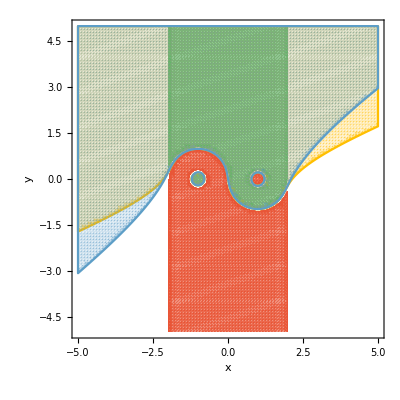

```mathematica
benchmarkname = "2d_ex2mod";
Print[benchmarkname];
verifytimelimit=600; (*verification time limit*)
plot =1; (*whether to plot(=1) or not (=0)*)
plotRange = {{-5,5},{-5,5}};
verifyResults[benchmarkname,plot,plotRange,verifytimelimit];
```

2d_ex3

x Variables: {x,y}

y Variables: {z1}

z Variables: {z2}

S1: {{-1.-1.21 x^4+y^4}}

S2: {{-1.+0.81 x^6-y^6}}

Verifying results (CAV20 method)...

{}{}

Valid solution.

h0.984173-1.02319 x^2-0.591482 x^4-3.14379 x^6-0.35575 y^2-0.387321 x^2 y^2-0.833695 x^4 y^2+0.400201 y^4+1.72129 x^2 y^4+2.16138 y^6

SDP Time: 0.015004

verify Time: 0.572445

Total Time: 0.587449

Verifying results (homogenization)...

Valid solution.

hHomo:4.32654-5.36321 x^2-1.73735 x^4-13.5209 x^6-1.36149 y^2-0.113625 x^2 y^2-2.38824 x^4 y^2+1.04621 y^4+5.0129 x^2 y^4+10.6467 y^6

SDP Time: 0.339496

verify Time: 0.592337

Total Time: 0.931833

Plot2d...

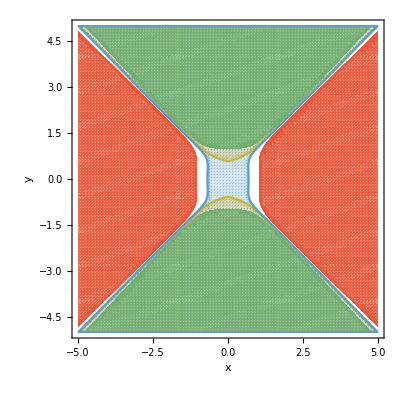

```mathematica
benchmarkname = "2d_ex3";
Print[benchmarkname];
verifytimelimit=1; (*verification time limit*)
plot =1; (*whether to plot(=1) or not (=0)*)
plotRange = {{-5,5},{-5,5}};
verifyResults[benchmarkname,plot,plotRange,verifytimelimit];
```

### 3-d benchmarks

```mathematica
benchmarkname = "example3d";
Print[benchmarkname];
verifytimelimit=600; (*verification time limit*)
plot =1; (*whether to plot(=1) or not (=0)*)
plotRange = {{-2,2},{-2,2},{-2,2}};
verifyResults[benchmarkname,plot,plotRange,verifytimelimit];
```

example3d

x Variables: {x,y,z}

y Variables: {a1,b1,c1,d1}

z Variables: {a2,b2,c2,d2}

S1: {4.-a1^2-b1^2-c1^2-d1^2-x^2-y^2-z^2,-0.01-a1^4+2. x^4-y^4,-1.-b1^2-c1^2-d1^2-x+z^2}

S2: {4.-a2^2-b2^2-c2^2-d2^2-x^2-y^2-z^2,-3.-a2-b2-d2^2+x^2-y,x}

Verifying results (CAV20 method)...

{{x→0,y→0,z→0,a1→0,b1→0,c1→0,d1→0}}{{x→0,y→0,z→0,a2→0,b2→0,c2→0,d2→0}}

Numerical Errors Detected. Invalid Solution.

SDP Time: 0.452697

verify Time: 0.004845

Total Time: 0.457542

Verifying results (homogenization)...

Valid solution.

hHomo:-0.000291904 x-0.50319 x^2-0.0000102561 x y-0.619259 y^2-0.407167 z^2

SDP Time: 0.868077

verify Time: 0.00216

Total Time: 0.870237

Plot3D...

$Aborted

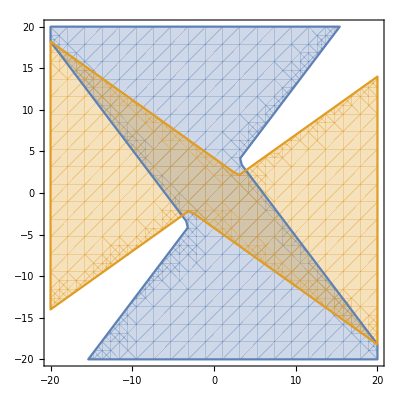

```mathematica
RegionPlot[{Or[(y-3(1+e))^2-(1+e)^2(x-3)^2≥ 0, (y+3*(1+e))^2-(1+e)^2(x+3)^2≥  0],
Or[(y-3(1-e))^2-(1-e)^2(x-3)^2≤  0, (y+3*(1-e))^2-(1-e)^2(x+3)^2≤   0]}
,{x,-20,20},{y,-20,20}]
```

```mathematica
s1 = {{x,y},{z,w}};
```

(x≥0&&y≥0)||(z≥0&&w≥0)

```mathematica
getRegionSAS[{x,y}]
```

x≥0&&y≥0

$Aborted